Predicted missile launch position:

{-385054,0}

Predicted missile trajectory:

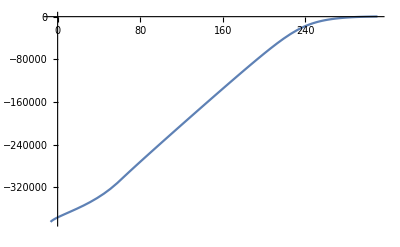

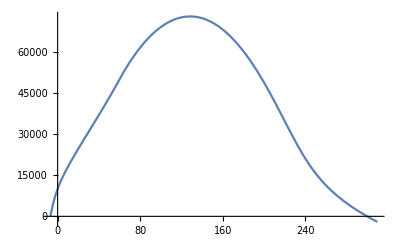

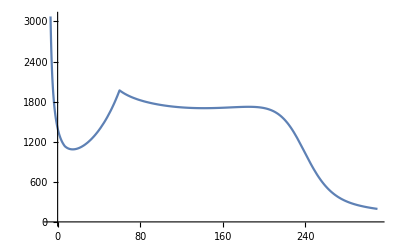

```mathematica
Rtlz[x_]:=Rationalize[x,0]
Pw[x_,y_,c_]:=Simplify[Piecewise[{{x,c},{y,Not[c]}}]]
ϵ=1/1000;

m=13800;
ρ=Rtlz[1.225];
H=10400;
Cd=1;
A=21/10;
ex=2000;
mfr=130;
b=68;
tt=15;
G=Rtlz[6.67408*10^(-11)];
M=Rtlz[5.972*10^24];
R=6371000;

t1=0;
t2=300;
v1=1400;
v2=800;
h0=0;
h1=10000;
h2=0;
d2=0;

ti=-8;
tf=t2+10;
hmax=100000;

Val[x_,s_]:=(x/.s)[[1]]
SpeedSq[t_]:=x'[t]^2+y'[t]^2
FixedSpeed[t_]:=Sqrt[ϵ+SpeedSq[t]];

𝕞=Pw[m-mfr*(t-ti),m-mfr*b,t<ti+b];
Thrust[t_]:=Pw[(1-Exp[ti-t])ex*mfr,0,t<ti+b];
FVx[t_]:=x'[t]/FixedSpeed[t]
FThrustx[t_]:=Pw[1,FVx[t],t<ti+tt]
FVy[t_]:=y'[t]/FixedSpeed[t]
FThrusty[t_]:=Pw[0,FVy[t],t<ti+tt]
DragCoeff[t_]:=1/2*ρ*Exp[-y[t]/H]*Cd*A;

eqs={𝕞*x''[t]==Thrust[t]*FThrustx[t]-DragCoeff[t]*x'[t]*FixedSpeed[t],𝕞*y''[t]==-G*M*𝕞/(R+y[t])^2+Thrust[t]*FThrusty[t]-DragCoeff[t]*y'[t]*FixedSpeed[t]};
s=NDSolve[{eqs,y[t1]==h1,SpeedSq[t1]==v1^2,x[t2]==d2,y[t2]==h2},{x,y},{t,ti,tf},AccuracyGoal->20,PrecisionGoal->10];

Off[NSolve::ifun];
t0=NSolve[Val[y[t],s]==h0,t][[1]][[1]][[2]];

"Predicted missile launch position:"
{Round[Val[x[t0],s]],Round[Val[y[t0],s]]}

"Predicted missile trajectory:"
Marker[x_,y_,s_]:=Graphics[{Line[{{x-s,y},{x+s,y}}],Line[{{x,y-s},{x,y+s}}]}];
plt=Plot[-h0-h1-h2,{X,Val[x[ti],s],Val[x[tf],s]},PlotRange->{Min[h0,h2],hmax},AxesStyle->{Directive[1/10,Black],Directive[0,Black]},Ticks->None,Axes->{True,False}];
Animate[Show[plt,ParametricPlot[{x[z],y[z]}/.s,{z,t0,t},PlotStyle->Red,PlotRange->40,PlotPoints->40],Marker[x[t1],y[t1],m/2],Graphics[{Blue,Rotate[Rectangle[{x[t]-m,y[t]-m/4},{x[t]+m,y[t]+m/4}],ArcTan[x'[t],y'[t]]]}],AspectRatio->Automatic]/.s,{t,ti,tf},AnimationRate->60, AnimationRunning->False,RefreshRate->120]
Plot[x[t]/.s,{t,t0,tf}]
Plot[y[t]/.s,{t,t0,tf}]
Plot[Sqrt[SpeedSq[t]]/.s,{t,t0,tf}]
```